# Homework 2 Homework Assignment 2

## Functions

plotScaffold function plots a scaffold path. 
path defines a scaffold folding path that consists of list of subpaths that each moves back and forth in x axis, along the same forward or backward direction in y axis. Each subpath consists a list of numbers of nucleotides in each subsequent scaffold domain between two adjacent crossovers. In other words, the path is assumed to zig-zag first up for a while, then down for a while, then up, down, etc.  The first upward zig-zag (i.e. a subpath) is specified by a list of how many nucleotides to go to the left, then how many to the right, then to the left, etc. The next list gives the subsequent downward zig-zag lengths, starting with a scaffold domain that is simultaneously the last domain of the previous subpath (but not included in the previous list).  And so on.
displayDomainType is an option that allows the scaffold domains to be shown in distinct colors based on the crossover orientations. The default is False. 
displayGrid is an option that allows the scaffold to be shown on top of a grid of helix turns (gridType→“helixTurn”) or staple columns (gridType→“stapleColumn”).
crossoverGap is an option that allows a pair of crossovers at adjacent nucleotide locations to be displayed with a gap. This is for clearer visualization of the scaffold path, at the cost of slight inaccuracy in crossover locations. The recommendation is to set crossoverGap→0 when displayGrid→True.

```mathematica
Options[plotScaffold]={displayDomainType->False,type1Color->Blue,type2Color->Orange,displayGrid->False,gridType->"helixTurn",gridColor->Lighter[Gray,0.8],gridLineColor->Lighter[Gray,0.5],lineThickness->1,crossoverGap->1};
plotScaffold[path_,OptionsPattern[]]:=Module[
{turn=10+2/3,bpLength=0.34,helixWidth=2,helixGap=1,columnWidth=16,
x1=0,y1=0,x2=0,y2=0,dx,dy,color,line,scaffold,gridWidth,gridLabel,
xMin=0,xMax=0,yMin=0,yMax=0},
dx=bpLength;
dy=-(helixWidth+helixGap);
scaffold=Table[
dy=-dy;
Table[
dx=-dx;
x1=x2;x2=x2+dx*path[[i,j]];If[x2<xMin,xMin=x2];If[x2>xMax,xMax=x2];
y1=y2;y2=y2+dy;If[y2<yMin,yMin=y2];If[y2>yMax,yMax=y2];
color=If[OptionValue[displayDomainType],
Which[
i==1&&j==1,Black,
i==Length[path]&&j==Length[path[[i]]],Black,
i>1&&j==1,OptionValue[type1Color],
True,OptionValue[type2Color]
],
Black];
line={{color,Line[{{x1+dx*OptionValue[crossoverGap],y1},{x2-dx*OptionValue[crossoverGap],y1}}]},
If[i!=Length[path]||j!=Length[path[[i]]],{Black,Line[{{x2-dx*OptionValue[crossoverGap],y1},{x2-dx*OptionValue[crossoverGap],y2}}]}]};
{AbsoluteThickness[OptionValue[lineThickness]],line},
{j,Length[path[[i]]]}],
{i,Length[path]}];
gridWidth=Switch[OptionValue[gridType],"helixTurn",turn,"stapleColumn",columnWidth];
gridLabel="grid type = "<>Switch[OptionValue[gridType],"helixTurn","helix turn","stapleColumn","staple column"];
Legended[Labeled[Graphics[
{If[OptionValue[displayGrid],
Table[{OptionValue[gridColor],EdgeForm[OptionValue[gridLineColor]],
Rectangle[{i*gridWidth*bpLength,(j+1/2)*(helixWidth+helixGap)},
{(i+1)*gridWidth*bpLength,(j+3/2)*(helixWidth+helixGap)}]},
{i,xMin/gridWidth/bpLength,Ceiling[xMax/gridWidth/bpLength]-1},
{j,Floor[yMin/3],Ceiling[yMax/3]-1}]],
scaffold}],
If[OptionValue[displayGrid],gridLabel,""],Top],
If[OptionValue[displayDomainType],SwatchLegend[{OptionValue[type1Color],OptionValue[type2Color]},{"between same-orientation crossovers","between different-orientation crossovers"}]]]]
```

repeat function generates a sequence of repeating elements. 
m defines the element. 
n defines the number of repeats.

```mathematica
repeat[m_,n_]:=Sequence@@ConstantArray[m,n]
```

# Homework 2.1 Calculate a scaffold path

Calculating number of rows of helices, bp per helix, etc.

Lengths of the sides of the square are equal and there are 7249 total bp we can use

Length: 0.34 nm/bp * 10.67 bp/turn * x turns = 3 nm/helix * y helices

7249 bp = y helices * 10.67 bp/turn * x turns/helix

```mathematica
turn=10+2/3;
x=Sqrt[7249/turn/0.34/turn*3]
bp=x*turn
length=bp*0.34
area=length*length
rows=length/3
```

23.71

252.907

85.9883

7393.98

28.6628

The square can be increased because the holes don’t use bp:

```mathematica
reduction=Sqrt[1-0.13];
newlength=length/reduction;
newbp=newlength/0.34;
newrows=newlength/3;
newarea=newlength*newlength;
newturns=newbp/turn
newbp
newlength
newarea
newrows
```

25.4198

271.144

92.1891

8498.83

30.7297

Number of turns and bp in longest helix that will work:
Has to be an odd number of turns, so 25 turns works for that.
Has to have and odd number of staple columns (multiple of 1.5 turns) between scaffold crossovers , so 25 does not work for that.
24 would work for odd number of staple columns (10.5, 13.5), but it is not odd.
The next number that works is 21 turns, 224 bp total, with 10.5, 10.5 turns for the scaffold crossovers.

Define a list of subpaths composing the full scaffold path (see definition of a path under Functions)

{21,10.5,10.5,10.5,10.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,4.5,2.5,2.5,3.5,3.5,4.5,4.5,5.5,5.5,10.5,10.5,10.5,10.5,10.5}

{{112,112,112,112,112,59,59,48,48,37,37,27,27,48,48,48,48,48,48,48,48,48,48},{96,16,16,16,16,16,16,48,48,48,48,27,27,37,37,27},{85,59,69,69,59,59,80,80,80,80,48,48,48,48,48,48,80,176,112,112,112,112},{224,112,112,112,112,48,48,48,48,48,48,48,48,48,48,48,48,27,27,37,37,48,48,59,59,112,112,112,112,112}}

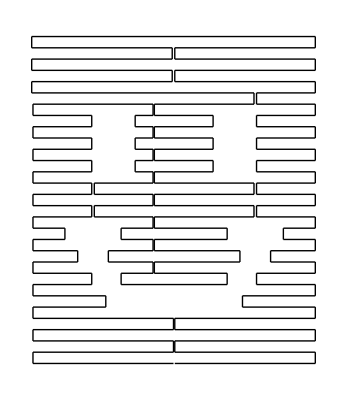

```mathematica
subpath[1]={repeat[10.5,5],repeat[5.5,2],repeat[4.5,2],repeat[3.5,2],repeat[2.5,2],repeat[4.5,4],repeat[4.5,6]};
subpath[2]={9,repeat[1.5,6],repeat[4.5,4],repeat[2.5,2],repeat[3.5,2],2.5};
subpath[3]={8,5.5,repeat[6.5,2],repeat[5.5,2],repeat[7.5,4],repeat[4.5,6],7.5,16.5,repeat[10.5,4]};
subpath[4]={21,repeat[10.5,4],repeat[4.5,2],repeat[4.5,6],repeat[4.5,4],repeat[2.5,2],repeat[3.5,2],repeat[4.5,2],repeat[5.5,2],repeat[10.5,5]}
path=Round[Table[subpath[i],{i,4}]*turn]
plotScaffold[path]
```

Display the scaffold path with domains in distinct colors based on the crossover orientations, and overlaid on top of a grid of helix turns. This enables verification of a correct design: a scaffold domain between two crossovers facing in the same orientation should have an integer number of turns; a scaffold domain between two crossovers facing in different orientations should have an integer number plus half a turn.

If any mistakes were identified, revise your design and repeat the above verification.

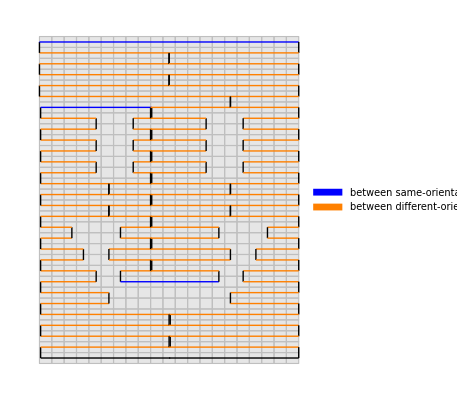
-Graphics-grid type = helix turn

```mathematica
plotScaffold[path,displayDomainType->True,displayGrid->True,gridType->"helixTurn",crossoverGap->0]
```

Display the scaffold path overlaid on top of a grid of staple columns. Evaluate if the design has a maximum number of scaffold domains whose length is an integer number of staple columns -- this feature will allow straightforward staple design.

If any possible improvements were identified, revise you design and repeat the above verification and optimization steps.

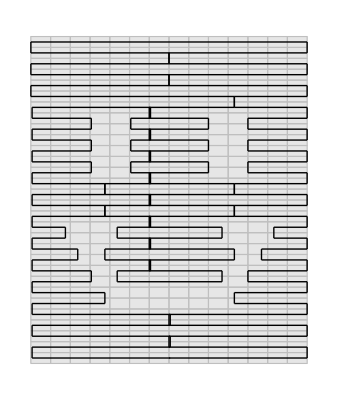
-Graphics-grid type = staple column

```mathematica
plotScaffold[path,crossoverGap->0,displayGrid->True,gridType->"stapleColumn"]
```

# Homework 2.2 Implement the design in scadnano

I used a python script to generate some of the scadnano file, but then went into scadnano and fixed some of the scaffold and made most of the staples.
See Homework2_2.py
Homework2_scadnano_code.sc is the file generated from the python code and is not the final design (not submitted, but complied from the python file)
See Homework2_scadnano_no_twist.sc and Homework2_scadnano_twist_deletion.sc for the final designs

# Homework 2.3 Analyze the design in CanDo

No twist corrections

```mathematica
-Graphics--Graphics--Graphics-
```

Twist corrections

```mathematica
-Graphics--Graphics--Graphics-
```

By adding the twist correction deletions, we improved the amount of twist in the design.
In the movies, there was also a lot less fluctuation in the designs with twist correction.